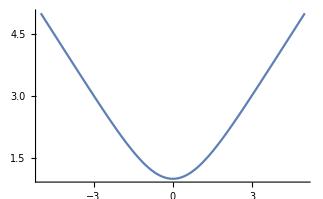

```mathematica
Plot[x/Tanh[x],{x,-5,5}]
```

```mathematica
beta[x_] := x/Tanh[x]
Limit[beta[x], x->0]
```

1

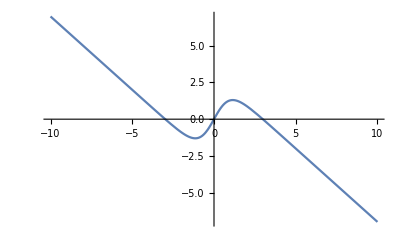

```mathematica
Plot[-x+3*Tanh[x], {x,-10,10}]
```

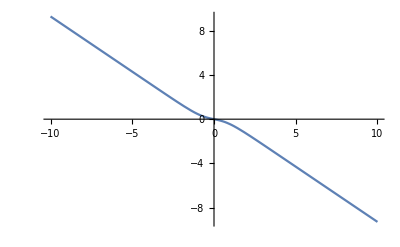

```mathematica
Plot[-x+0.7*Tanh[x], {x,-10,10}]
```

```mathematica
Integrate[Cos[3*x]*Exp[x/2],x]
```

2/37 ⅇ^(x/2) (Cos[3 x]+6 Sin[3 x])

{{v→InterpolatingFunction[{{0., 10.}}, <>]}}

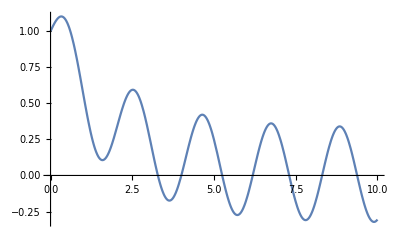

{-0.305731}

```mathematica
f[v_,t_]:=Cos[3*t]-v/2
sol = NDSolve[{v'[t]==f[v[t],t], v[0]==1},v, {t,0,10}]
Plot[Evaluate[v[t]/.sol], {t,0,10}, PlotRange->All]
v[10]/.sol
```

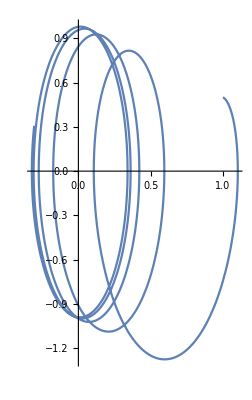

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
ParametricPlot[Evaluate[{v[t],v'[t]}/.sol],{t,0,10}]
```